```mathematica
(λ2^2 n2-λ1^2 n1)/(λ2^2-λ1^2)/.λ1->390 10^-9/.λ2->730 10^-9/.n1->1.341/.n2->1.326
```

1.32001

```mathematica
(n1-n2)/(1/λ1^2-1/λ2^2)/.λ1->390 10^-9/.λ2->730 10^-9/.n1->1.341/.n2->1.326
```

3.19278×10^-15

```mathematica
(π+2ArcCos[√((n^2-1)/3)]-4ArcSin[1/n √((4-n^2)/3)])/π/.n->{1.32,1.5}
```

{0.755517,0.873103}

```mathematica
(2π-4ArcSin[1/n])/π/.n->{1.32,1.5}
```

{0.905535,1.07088}

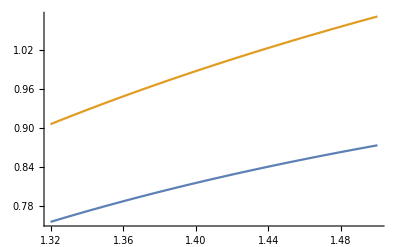

```mathematica
Plot[{(π+2ArcCos[√((n^2-1)/3)]-4ArcSin[1/n √((4-n^2)/3)])/π,(2π-4ArcSin[1/n])/π},{n,1.32,1.5}]
```

```mathematica
(2π+2ArcCos[√((n^2-1)/8)]-6ArcSin[1/n √((9-n^2)/8)])/π/.n->{1.32,1.5}
```

{1.26346,1.48258}

```mathematica
(3π-6ArcSin[1/n])/π/.n->{1.32,1.5}
```

{1.3583,1.60632}

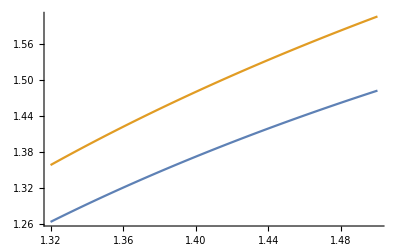

```mathematica
Plot[{(2π+2ArcCos[√((n^2-1)/8)]-6ArcSin[1/n √((9-n^2)/8)])/π,(3π-6ArcSin[1/n])/π},{n,1.32,1.5}]
```

Doesn't seem to intercept ..
even if consider backward rays, then one of the plots is turned upside down, nevertheless they don’t intercept..

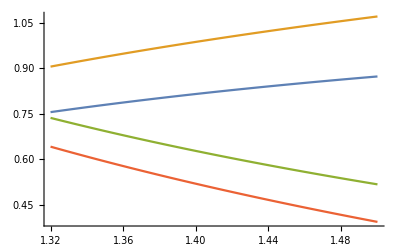

```mathematica
Plot[{(π+2ArcCos[√((n^2-1)/3)]-4ArcSin[1/n √((4-n^2)/3)])/π,(2π-4ArcSin[1/n])/π,2-(2π+2ArcCos[√((n^2-1)/8)]-6ArcSin[1/n √((9-n^2)/8)])/π,2-(3π-6ArcSin[1/n])/π},{n,1.32,1.5}]
```